```mathematica
Needs["PlotLegends`"]
```

```mathematica
g1k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/1k.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/10k.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/20k.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/30k.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/40k.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/50k.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g75k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/75k.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g100k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/100k.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
```

```mathematica
g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/l1e4-all-2.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/l2e4-all-4M.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g30k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/l3e4-all2.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/l4e4-all2.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g50k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/l5e4-all2.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g75k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/l7.5e4-all2.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g100k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/l10e4-all.2M.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
```

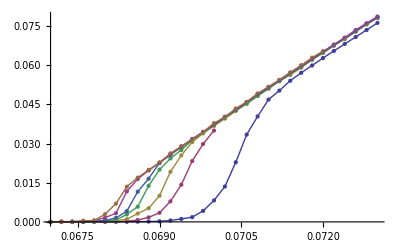

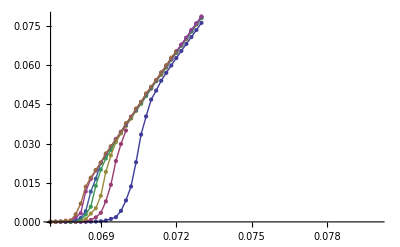

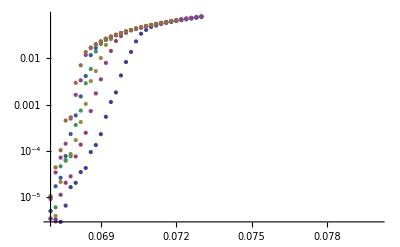

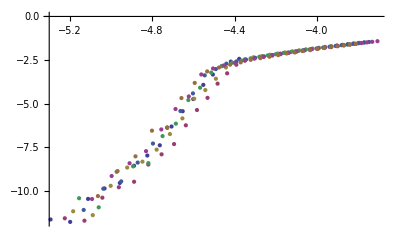

ListPlot[{{{-5.29357,-11.6455},{-5.19826,-11.7834},{-5.11125,-10.4643},{-5.03121,-9.86493},{-4.9571,-9.54979},{-4.88811,-8.56258},{-4.82357,-7.97651},{-4.76295,-7.38912},{-4.70579,-6.31306},{-4.65172,-5.43547},{-4.60043,-4.73717},{-4.55164,-3.92357},{-4.50512,-3.33093},{-4.46066,-2.83711},{-4.41811,-2.59068},{-4.37728,-2.43124}},{{-5.22426,-11.5761},{-5.12895,-11.7141},{-5.04194,-10.395},{-4.9619,-9.79561},{-4.88779,-9.48047},{-4.81879,-8.49327},{-4.75426,-7.90719},{-4.69363,-7.31981},{-4.63647,-6.24375},{-4.58241,-5.36616},{-4.53111,-4.66785},{-4.48232,-3.85426},{-4.4358,-3.26162},{-4.39135,-2.76779},{-4.34879,-2.52136},{-4.30797,-2.36192}},{{-5.18371,-11.1742},{-5.0884,-11.3963},{-5.00139,-9.71387},{-4.92135,-8.66656},{-4.84724,-8.32881},{-4.77825,-7.63815},{-4.71371,-6.74548},{-4.65308,-5.8457},{-4.59593,-4.71673},{-4.54186,-4.22104},{-4.49057,-3.5714},{-4.44178,-2.92288},{-4.39526,-2.63883},{-4.3508,-2.45704},{-4.30824,-2.35299},{-4.26742,-2.27245},{-4.2282,-2.19851},{-4.19046,-2.12717},{-4.15409,-2.06435},{-4.119,-2.00048},{-4.0851,-1.94492},{-4.05231,-1.88908},{-4.02056,-1.84598},{-3.98979,-1.79792},{-3.95994,-1.74815},{-3.93095,-1.70747},{-3.90278,-1.66476},{-3.87538,-1.62867},{-3.84871,-1.58797},{-3.82274,-1.55163},{-3.79742,-1.51913}},{{-5.15494,-10.4253},{-5.05963,-10.9474},{-4.97262,-8.90816},{-4.89258,-8.59706},{-4.81847,-8.41211},{-4.74948,-6.86228},{-4.68494,-6.1496},{-4.62432,-4.79463},{-4.56716,-4.08778},{-4.51309,-3.22261},{-4.4618,-2.85091},{-4.41301,-2.65696},{-4.36649,-2.53307},{-4.32204,-2.40332},{-4.27948,-2.31166},{-4.23865,-2.23197},{-4.19943,-2.16368},{-4.16169,-2.09026},{-4.12533,-2.0342},{-4.09023,-1.97115},{-4.05633,-1.91174},{-4.02354,-1.85894},{-3.99179,-1.80849},{-3.96102,-1.76171},{-3.93117,-1.71613},{-3.90218,-1.67606},{-3.87401,-1.63452},{-3.84661,-1.59338},{-3.81994,-1.5582},{-3.79397,-1.51945},{-3.76865,-1.48774}},{{-5.13263,-11.0976},{-5.03732,-9.8785},{-4.95031,-9.46015},{-4.87027,-8.38047},{-4.79616,-7.28898},{-4.72717,-6.36589},{-4.66263,-5.42406},{-4.602,-4.41347},{-4.54484,-3.3772},{-4.49078,-3.01878},{-4.43948,-2.70784},{-4.39069,-2.57976},{-4.34417,-2.46918},{-4.29972,-2.37244},{-4.25716,-2.2873},{-4.21634,-2.21084},{-4.17712,-2.1324},{-4.13938,-2.06815},{-4.10301,-1.99934},{-4.06792,-1.94066},{-4.03402,-1.88674},{-4.00123,-1.83687},{-3.96948,-1.78482},{-3.93871,-1.73989},{-3.90885,-1.6934},{-3.87987,-1.64911},{-3.8517,-1.60863},{-3.8243,-1.57159},{-3.79763,-1.53374},{-3.77165,-1.49629},{-3.74634,-1.46416}},{{-5.09208,-10.4708},{-4.99677,-9.15094},{-4.90976,-8.41863},{-4.82972,-7.72593},{-4.75561,-6.48079},{-4.68662,-5.30836},{-4.62208,-4.58718},{-4.56146,-3.32781},{-4.5043,-2.98541},{-4.45023,-2.80445},{-4.39894,-2.66398},{-4.35015,-2.53295},{-4.30363,-2.42119},{-4.25917,-2.32616},{-4.21662,-2.24434},{-4.17579,-2.16169},{-4.13657,-2.08899},{-4.09883,-2.0197},{-4.06246,-1.9595},{-4.02737,-1.89325},{-3.99347,-1.84011},{-3.96068,-1.78909},{-3.92893,-1.73811},{-3.89816,-1.69253},{-3.86831,-1.64909},{-3.83932,-1.60757},{-3.81115,-1.56659},{-3.78375,-1.52801},{-3.75708,-1.48738},{-3.73111,-1.45308},{-3.70579,-1.41949}},{{-5.06332,-10.3015},{-4.96801,-8.87154},{-4.88099,-8.02284},{-4.80095,-6.54982},{-4.72684,-6.39241},{-4.65785,-4.6801},{-4.59331,-3.8118},{-4.53269,-3.15354},{-4.47553,-2.92667},{-4.42146,-2.76469},{-4.37017,-2.63234},{-4.32138,-2.48898},{-4.27486,-2.39133},{-4.23041,-2.30779},{-4.18785,-2.21955},{-4.14702,-2.12315},{-4.1078,-2.06675},{-4.07006,-1.98511},{-4.0337,-1.92849},{-3.9986,-1.86046},{-3.9647,-1.80998},{-3.93191,-1.76189},{-3.90016,-1.71},{-3.86939,-1.663},{-3.83954,-1.61464},{-3.81055,-1.57602}}},PlotLegend→{1k,10k,20k,30k,40k,50k,75k,100k},LegendPosition→{1.1,-0.4},LegendShadow→None,Joined→{True},PlotMarkers→Automatic]

```mathematica
n=4;
ClearAll[d0,z,α];
d0=0.065;
z=0.1;
α=0.1;

gap1=Table[{g1k1[[All,1]][[j]],Sum[g1k1[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g1k1]}];
gap10=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g10k1]}];
gap20=Table[{g20k1[[All,1]][[j]],Sum[g20k1[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g20k1]}];
gap30=Table[{g30k1[[All,1]][[j]],Sum[g30k1[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g30k1]}];
gap40=Table[{g40k1[[All,1]][[j]],Sum[g40k1[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g40k1]}];
gap50=Table[{g50k1[[All,1]][[j]],Sum[g50k1[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g50k1]}];
gap75=Table[{g75k1[[All,1]][[j]],Sum[g75k1[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g75k1]}];
gap100=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g100k1]}];
pic1=ListPlot[{gap10,gap20,gap30,gap40,gap50,gap75,gap100}];
pic2=ListLinePlot[{gap10,gap20,gap30,gap40,gap50,gap75,gap100}];
Show[{pic1,pic2}]
pic3=ListPlot[{gap10,gap20,gap30,gap40,gap50,gap75,gap100},PlotRange->{{0.067,0.08},Full}];
pic4=ListLinePlot[{gap10,gap20,gap30,gap40,gap50,gap75,gap100},PlotRange->{{0.067,0.08},Full}];
Show[{pic3,pic4}]
pic7=ListLogPlot[{gap10,gap20,gap30,gap40,gap50,gap75,gap100},PlotRange->{{0.067,0.08},Full}]




ga1k1=gap1[[All,1]];
ga10k1=gap10[[All,1]];
ga20k1=gap20[[All,1]];
ga30k1=gap30[[All,1]];
ga40k1=gap40[[All,1]];
ga50k1=gap50[[All,1]];
ga75k1=gap75[[All,1]];
ga100k1=gap100[[All,1]];
ga1k2=gap1[[All,2]];
ga10k2=gap10[[All,2]];
ga20k2=gap20[[All,2]];
ga30k2=gap30[[All,2]];
ga40k2=gap40[[All,2]];
ga50k2=gap50[[All,2]];
ga75k2=gap75[[All,2]];
ga100k2=gap100[[All,2]];

g1k=Table[{Log[ga1k1[[i]]-d0]+z*Log[1*1000.],
Log[ga1k2[[i]]]+α*Log[1*1000.]},{i,1,Length[ga1k1]}];
g10k=Table[{Log[ga10k1[[i]]-d0]+z*Log[10*1000.],
Log[ga10k2[[i]]]+α*Log[10*1000.]},{i,1,Length[ga10k1]}];

g20k=Table[{Log[ga20k1[[i]]-d0]+z*Log[20*1000.],Log[ga20k2[[i]]]+α*Log[20*1000.]},{i,1,Length[ga20k1]}];
g30k=Table[{Log[ga30k1[[i]]-d0]+z*Log[30*1000.],Log[ga30k2[[i]]]+α*Log[30*1000.]},{i,1,Length[ga30k1]}];
g40k=Table[{Log[ga40k1[[i]]-d0]+z*Log[40*1000.],Log[ga40k2[[i]]]+α*Log[40*1000.]},{i,1,Length[ga40k1]}];
g50k=Table[{Log[ga50k1[[i]]-d0]+z*Log[50*1000.],Log[ga50k2[[i]]]+α*Log[50*1000.]},{i,1,Length[ga50k1]}];
g75k=Table[{Log[ga75k1[[i]]-d0]+z*Log[75*1000.],Log[ga75k2[[i]]]+α*Log[75*1000.]},{i,1,Length[ga75k1]}];
g100k=Table[{Log[ga100k1[[i]]-d0]+z*Log[100*1000.],Log[ga100k2[[i]]]+α*Log[100*1000.]},{i,1,Length[ga100k1]}];
ListPlot[{g10k,g20k,g30k,g40k,g50k,g75k,g100k},PlotRange->Full]
ListPlot[{g10k,g20k,g30k,g40k,g50k,g75k,g100k},PlotLegend->{"1k","10k","20k","30k","40k","50k","75k","100k"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->{True},PlotMarkers->Automatic]
```

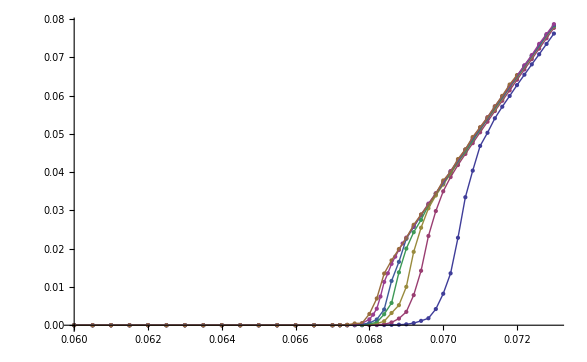

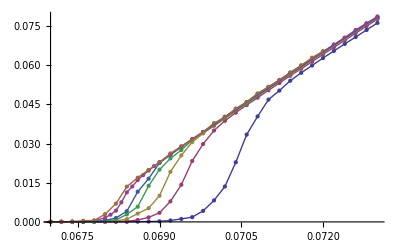

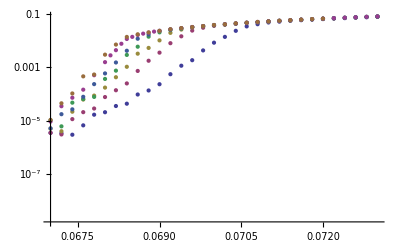

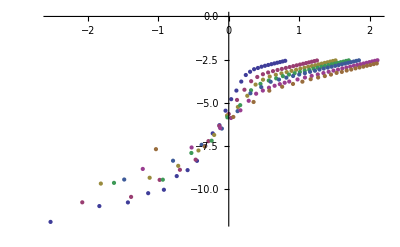

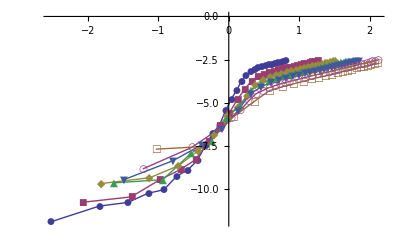

```mathematica
0.9
```

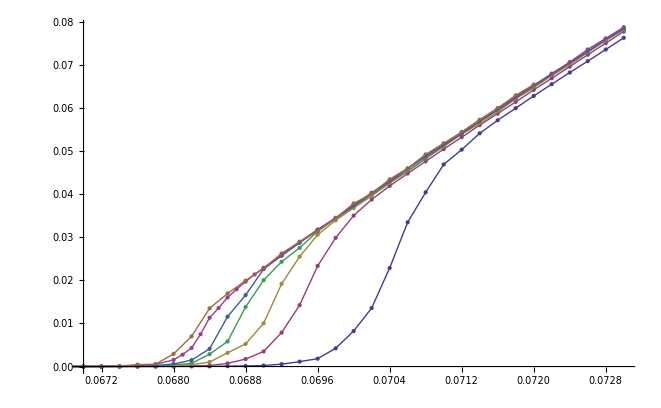

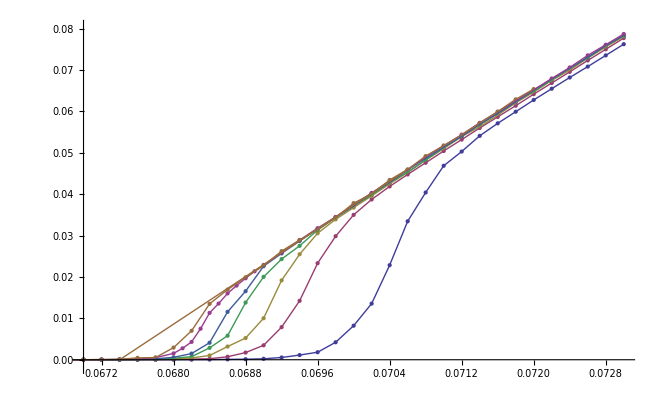

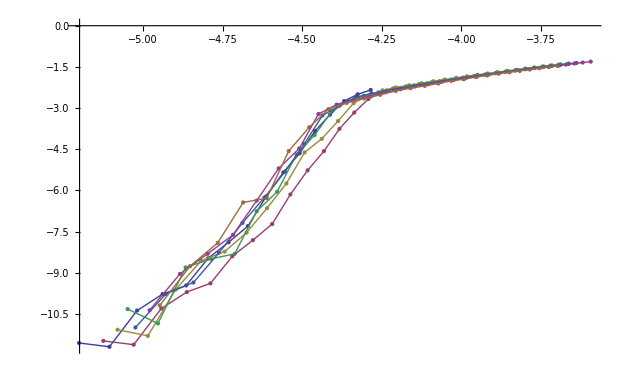

ListPlot[{{{-5.20147,-11.5533},{-5.10616,-11.6913},{-5.01915,-10.3722},{-4.93911,-9.77283},{-4.865,-9.45768},{-4.79601,-8.47048},{-4.73147,-7.8844},{-4.67084,-7.29702},{-4.61368,-6.22096},{-4.55962,-5.34337},{-4.50832,-4.64506},{-4.45953,-3.83147},{-4.41301,-3.23883},{-4.36856,-2.745},{-4.326,-2.49857},{-4.28518,-2.33914}},{{-5.12522,-11.4771},{-5.02991,-11.6151},{-4.9429,-10.2959},{-4.86286,-9.69658},{-4.78875,-9.38144},{-4.71976,-8.39423},{-4.65522,-7.80816},{-4.5946,-7.22077},{-4.53744,-6.14471},{-4.48337,-5.26713},{-4.43208,-4.56882},{-4.38329,-3.75523},{-4.33677,-3.16258},{-4.29232,-2.66876},{-4.24976,-2.42233},{-4.20893,-2.26289}},{{-5.08062,-11.0711},{-4.98531,-11.2932},{-4.8983,-9.61078},{-4.81826,-8.56347},{-4.74415,-8.22572},{-4.67516,-7.53506},{-4.61062,-6.64239},{-4.55,-5.74261},{-4.49284,-4.61364},{-4.43877,-4.11795},{-4.38748,-3.46831},{-4.33869,-2.81979},{-4.29217,-2.53574},{-4.24771,-2.35395},{-4.20515,-2.2499},{-4.16433,-2.16936},{-4.12511,-2.09542},{-4.08737,-2.02408},{-4.051,-1.96126},{-4.01591,-1.89739},{-3.98201,-1.84183},{-3.94922,-1.78599},{-3.91747,-1.74289},{-3.8867,-1.69483},{-3.85685,-1.64506},{-3.82786,-1.60438},{-3.79969,-1.56167},{-3.77229,-1.52558},{-3.74562,-1.48488},{-3.71965,-1.44854},{-3.69433,-1.41604}},{{-5.04898,-10.3193},{-4.95367,-10.8414},{-4.86666,-8.8022},{-4.78661,-8.49109},{-4.71251,-8.30614},{-4.64351,-6.75631},{-4.57897,-6.04364},{-4.51835,-4.68867},{-4.46119,-3.98182},{-4.40712,-3.11664},{-4.35583,-2.74494},{-4.30704,-2.55099},{-4.26052,-2.42711},{-4.21607,-2.29736},{-4.17351,-2.20569},{-4.13269,-2.12601},{-4.09347,-2.05772},{-4.05573,-1.9843},{-4.01936,-1.92823},{-3.98427,-1.86519},{-3.95037,-1.80577},{-3.91758,-1.75298},{-3.88583,-1.70252},{-3.85506,-1.65575},{-3.8252,-1.61017},{-3.79622,-1.5701},{-3.76804,-1.52856},{-3.74065,-1.48741},{-3.71398,-1.45224},{-3.688,-1.41349},{-3.66268,-1.38177}},{{-5.02443,-10.9894},{-4.92912,-9.7703},{-4.84211,-9.35195},{-4.76207,-8.27227},{-4.68796,-7.18079},{-4.61897,-6.25769},{-4.55443,-5.31586},{-4.4938,-4.30527},{-4.43665,-3.269},{-4.38258,-2.91058},{-4.33129,-2.59965},{-4.2825,-2.47156},{-4.23598,-2.36098},{-4.19152,-2.26424},{-4.14896,-2.1791},{-4.10814,-2.10264},{-4.06892,-2.0242},{-4.03118,-1.95995},{-3.99481,-1.89115},{-3.95972,-1.83247},{-3.92582,-1.77855},{-3.89303,-1.72867},{-3.86128,-1.67662},{-3.83051,-1.63169},{-3.80066,-1.5852},{-3.77167,-1.54091},{-3.7435,-1.50043},{-3.7161,-1.46339},{-3.68943,-1.42554},{-3.66346,-1.38809},{-3.63814,-1.35596}},{{-4.97983,-10.3585},{-4.88452,-9.03868},{-4.79751,-8.30638},{-4.71747,-7.61368},{-4.64336,-6.36853},{-4.57437,-5.19611},{-4.50983,-4.47493},{-4.4492,-3.21556},{-4.39204,-2.87316},{-4.33798,-2.6922},{-4.28668,-2.55173},{-4.23789,-2.4207},{-4.19137,-2.30894},{-4.14692,-2.21391},{-4.10436,-2.13209},{-4.06354,-2.04944},{-4.02432,-1.97674},{-3.98658,-1.90744},{-3.95021,-1.84725},{-3.91512,-1.78099},{-3.88122,-1.72786},{-3.84843,-1.67684},{-3.81668,-1.62586},{-3.78591,-1.58027},{-3.75606,-1.53683},{-3.72707,-1.49532},{-3.6989,-1.45434},{-3.6715,-1.41575},{-3.64483,-1.37512},{-3.61885,-1.34083},{-3.59354,-1.30724}},{{-4.94819,-10.1864},{-4.85288,-8.75641},{-4.76586,-7.90771},{-4.68582,-6.43469},{-4.61171,-6.27728},{-4.54272,-4.56497},{-4.47818,-3.69667},{-4.41756,-3.03841},{-4.3604,-2.81154},{-4.30633,-2.64956},{-4.25504,-2.51721},{-4.20625,-2.37385},{-4.15973,-2.2762},{-4.11528,-2.19266},{-4.07272,-2.10442},{-4.0319,-2.00802},{-3.99267,-1.95162},{-3.95493,-1.86998},{-3.91857,-1.81336},{-3.88348,-1.74533},{-3.84957,-1.69485},{-3.81678,-1.64676},{-3.78504,-1.59487},{-3.75426,-1.54787},{-3.72441,-1.49951},{-3.69542,-1.46089}}},PlotLegend→{10k,20k,30k,40k,50k,75k,100k},LegendPosition→{1.1,-0.4},LegendShadow→None,Joined→{True},PlotMarkers→Automatic]

```mathematica
ClearAll[d0,z,α];
d0=0.065;
z=0.11;
α=0.11;
g1k=Table[{Log[ga1k1[[i]]-d0]+z*Log[1*1000.],
Log[ga1k2[[i]]]+α*Log[1*1000.]},{i,1,Length[ga1k1]}];
g10k=Table[{Log[ga10k1[[i]]-d0]+z*Log[10*1000.],
Log[ga10k2[[i]]]+α*Log[10*1000.]},{i,1,Length[ga10k1]}];

g20k=Table[{Log[ga20k1[[i]]-d0]+z*Log[20*1000.],Log[ga20k2[[i]]]+α*Log[20*1000.]},{i,1,Length[ga20k1]}];
g30k=Table[{Log[ga30k1[[i]]-d0]+z*Log[30*1000.],Log[ga30k2[[i]]]+α*Log[30*1000.]},{i,1,Length[ga30k1]}];
g40k=Table[{Log[ga40k1[[i]]-d0]+z*Log[40*1000.],Log[ga40k2[[i]]]+α*Log[40*1000.]},{i,1,Length[ga40k1]}];
g50k=Table[{Log[ga50k1[[i]]-d0]+z*Log[50*1000.],Log[ga50k2[[i]]]+α*Log[50*1000.]},{i,1,Length[ga50k1]}];
g75k=Table[{Log[ga75k1[[i]]-d0]+z*Log[75*1000.],Log[ga75k2[[i]]]+α*Log[75*1000.]},{i,1,Length[ga75k1]}];
g100k=Table[{Log[ga100k1[[i]]-d0]+z*Log[100*1000.],Log[ga100k2[[i]]]+α*Log[100*1000.]},{i,1,Length[ga100k1]}];
pic5=ListPlot[{g10k,g20k,g30k,g40k,g50k,g75k,g100k},PlotRange->Full];
pic6=ListLinePlot[{g10k,g20k,g30k,g40k,g50k,g75k,g100k},PlotRange->Full];
Show[{pic5,pic6}]
ListPlot[{g10k,g20k,g30k,g40k,g50k,g75k,g100k},PlotLegend->{"10k","20k","30k","40k","50k","75k","100k"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->{True},PlotMarkers->Automatic]
```

```mathematica
n=10
gap1010=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,n+2,n+2}]},{j,1,Length[g10k1]}];
```

10

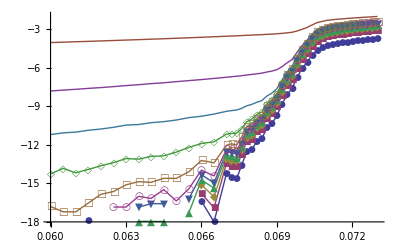

```mathematica
ListLogPlot[{gap100,gap101,gap102,gap103,gap104,gap105,gap106,gap107,gap108,gap109,gap1010},PlotLegend->{"0","1","2","3","4","5","6","7","8","9","10"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->{True},PlotMarkers->Automatic,PlotRange->Full]
```

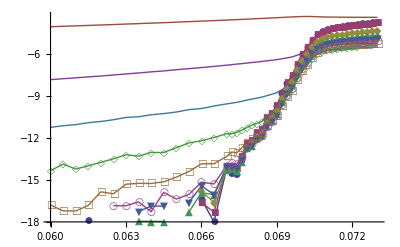

```mathematica
ListLogPlot[{gap100,gap101,gap102,gap103,gap104,gap105,gap106,gap107,gap108,gap109,gap1010},PlotLegend->{"0","1","2","3","4","5","6","7","8","9","10"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->{True},PlotMarkers->Automatic,PlotRange->Full]
```

```mathematica
n=0
gap1000=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,2}]},{j,1,Length[g100k1]}];
gap1001=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,3,3}]},{j,1,Length[g100k1]}];
gap1002=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,4,4}]},{j,1,Length[g100k1]}];
gap1003=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,5,5}]},{j,1,Length[g100k1]}];
gap1004=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,6,6}]},{j,1,Length[g100k1]}];
gap1005=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,7,7}]},{j,1,Length[g100k1]}];
gap1006=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,8,8}]},{j,1,Length[g100k1]}];
gap1007=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,9,9}]},{j,1,Length[g100k1]}];
gap1008=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,10,10}]},{j,1,Length[g100k1]}];
gap1009=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,11,11}]},{j,1,Length[g100k1]}];
gap10010=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,12,12}]},{j,1,Length[g100k1]}];
```

```mathematica
gapa1000=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,2}]},{j,1,Length[g100k1]}];
gapa1001=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,3}]},{j,1,Length[g100k1]}];
gapa1002=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,4}]},{j,1,Length[g100k1]}];
gapa1003=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,5}]},{j,1,Length[g100k1]}];
gapa1004=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,6}]},{j,1,Length[g100k1]}];
gapa1005=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,7}]},{j,1,Length[g100k1]}];
gapa1006=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,8}]},{j,1,Length[g100k1]}];
gapa1007=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,9}]},{j,1,Length[g100k1]}];
gapa1008=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,10}]},{j,1,Length[g100k1]}];
gapa1009=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,11}]},{j,1,Length[g100k1]}];
gapa10010=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,12}]},{j,1,Length[g100k1]}];
```

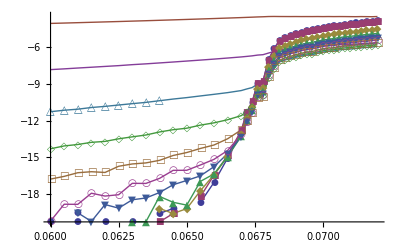

```mathematica
ListLogPlot[{gap1000,gap1001,gap1002,gap1003,gap1004,gap1005,gap1006,gap1007,gap1008,gap1009,gap10010},PlotLegend->{"0","1","2","3","4","5","6","7","8","9","10"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->{True},PlotMarkers->Automatic,PlotRange->Full]
```

```mathematica
ListLogPlot[{gapa1000,gapa1001,gapa1002,gapa1003,gapa1004,gapa1005,gapa1006,gapa1007,gapa1008,gapa1009,gapa10010},PlotLegend->{"0","1","2","3","4","5","6","7","8","9","10"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->{True},PlotMarkers->Automatic,PlotRange->Full]
```

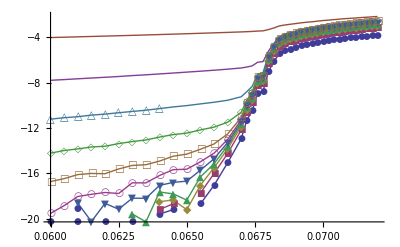

```mathematica
n=0
gap1000=Table[{g1k1[[All,1]][[j]],Sum[g1k1[[All,i]][[j]],{i,2,2}]},{j,1,Length[g1k1]}];
gap1001=Table[{g1k1[[All,1]][[j]],Sum[g1k1[[All,i]][[j]],{i,3,3}]},{j,1,Length[g1k1]}];
gap1002=Table[{g1k1[[All,1]][[j]],Sum[g1k1[[All,i]][[j]],{i,4,4}]},{j,1,Length[g1k1]}];
gap1003=Table[{g1k1[[All,1]][[j]],Sum[g1k1[[All,i]][[j]],{i,5,5}]},{j,1,Length[g1k1]}];
gap1004=Table[{g1k1[[All,1]][[j]],Sum[g1k1[[All,i]][[j]],{i,6,6}]},{j,1,Length[g1k1]}];
gap1005=Table[{g1k1[[All,1]][[j]],Sum[g1k1[[All,i]][[j]],{i,7,7}]},{j,1,Length[g1k1]}];
gap1006=Table[{g1k1[[All,1]][[j]],Sum[g1k1[[All,i]][[j]],{i,8,8}]},{j,1,Length[g1k1]}];
gap1007=Table[{g1k1[[All,1]][[j]],Sum[g1k1[[All,i]][[j]],{i,9,9}]},{j,1,Length[g1k1]}];
gap1008=Table[{g1k1[[All,1]][[j]],Sum[g1k1[[All,i]][[j]],{i,10,10}]},{j,1,Length[g1k1]}];
gap1009=Table[{g1k1[[All,1]][[j]],Sum[g1k1[[All,i]][[j]],{i,11,11}]},{j,1,Length[g1k1]}];
gap10010=Table[{g1k1[[All,1]][[j]],Sum[g1k1[[All,i]][[j]],{i,12,12}]},{j,1,Length[g1k1]}];
```

0

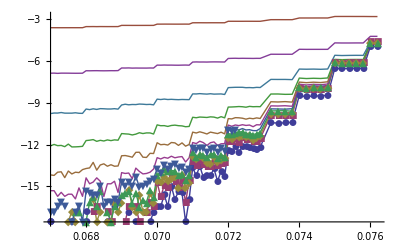

```mathematica
ListLogPlot[{gap1000,gap1001,gap1002,gap1003,gap1004,gap1005,gap1006,gap1007,gap1008,gap1009,gap10010},PlotLegend->{"0","1","2","3","4","5","6","7","8","9","10"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->{True},PlotMarkers->Automatic,PlotRange->Full]
```

```mathematica
g20k1
```

{{0.06,0,0,0,0,0,8.33333×10^-9,1/20000000,7.16667×10^-7,0.0000129167,0.000397325,0.0172476},{0.0605,0,0,0,0,0,2.47934×10^-8,4.95868×10^-8,6.36364×10^-7,0.0000142397,0.000420636,0.0177812},{0.061,0,0,0,0,0,0,6.55738×10^-8,7.62295×10^-7,0.0000158934,0.000454172,0.0183134},{0.0615,0,0,0,0,0,8.13008×10^-9,1.30081×10^-7,9.26829×10^-7,0.0000180813,0.000477984,0.0189127},{0.062,0,0,0,0,8.06452×10^-9,1.6129×10^-8,4.03226×10^-8,1.14516×10^-6,0.0000195242,0.00050996,0.0194999},{0.0625,0,0,0,0,0,3.2×10^-8,1.6×10^-7,1.336×10^-6,0.000021904,0.0005496,0.020146},{0.063,0,0,1.5873×10^-8,0,1.5873×10^-8,2.38095×10^-8,1.90476×10^-7,1.71429×10^-6,0.0000248333,0.000593341,0.0208181},{0.0635,0,0,0,0,1.5748×10^-8,6.29921×10^-8,2.12598×10^-7,1.92126×10^-6,0.0000283386,0.000638165,0.021537},{0.064,3.90625×10^-8,3.125×10^-8,6.25×10^-8,5.46875×10^-8,7.8125×10^-8,9.375×10^-8,3.35938×10^-7,2.57031×10^-6,0.0000308906,0.000685594,0.0222677},{0.0645,0,0,7.75194×10^-9,1.55039×10^-8,2.32558×10^-8,1.00775×10^-7,3.56589×10^-7,2.5814×10^-6,0.0000344884,0.000739597,0.0230681},{0.065,0,0,0,1.53846×10^-8,2.30769×10^-8,9.23077×10^-8,4.23077×10^-7,3.46923×10^-6,0.0000409308,0.000798615,0.0238587},{0.0655,7.63359×10^-8,9.16031×10^-8,1.29771×10^-7,8.39695×10^-8,1.9084×10^-7,2.1374×10^-7,9.31298×10^-7,4.14504×10^-6,0.0000449313,0.000862305,0.0247077},{0.066,9.09091×10^-8,1.13636×10^-7,1.13636×10^-7,1.43939×10^-7,1.89394×10^-7,3.10606×10^-7,7.19697×10^-7,5.15152×10^-6,0.0000521061,0.000933174,0.0256923},{0.0665,2.25564×10^-8,8.27068×10^-8,1.20301×10^-7,1.65414×10^-7,3.23308×10^-7,4.96241×10^-7,9.47368×10^-7,6.18045×10^-6,0.0000599699,0.00101623,0.0266911},{0.067,5.85821×10^-7,8.26493×10^-7,7.01493×10^-7,6.32463×10^-7,7.40672×10^-7,9.73881×10^-7,1.89552×10^-6,8.05597×10^-6,0.000070056,0.00110957,0.0277524},{0.0672,5.84077×10^-7,7.21726×10^-7,5.48735×10^-7,5.52455×10^-7,6.3058×10^-7,1.0119×10^-6,2.10193×10^-6,8.72396×10^-6,0.0000735956,0.00115117,0.0282102},{0.0674,2.45734×10^-6,2.91914×10^-6,2.17174×10^-6,1.97515×10^-6,1.83791×10^-6,2.1977×10^-6,3.25111×10^-6,0.0000103746,0.0000800964,0.00119018,0.028669},{0.0676,4.6912×10^-6,5.35318×10^-6,3.97374×10^-6,3.45784×10^-6,3.21191×10^-6,3.5503×10^-6,4.76146×10^-6,0.0000123928,0.0000860152,0.00123974,0.0291462},{0.0678,6.66667×10^-6,7.30826×10^-6,5.36504×10^-6,4.76954×10^-6,4.24226×10^-6,4.57227×10^-6,5.93658×10^-6,0.0000144211,0.0000930365,0.00129068,0.0296444},{0.068,0.0000187776,0.0000203217,0.0000143382,0.0000122335,0.0000104173,0.0000101471,0.0000108585,0.0000201801,0.000103173,0.0013453,0.0301482},{0.0682,0.0000352071,0.0000375678,0.0000259091,0.0000205993,0.0000174413,0.0000160502,0.0000167394,0.0000267632,0.000115086,0.00140279,0.0306737},{0.0684,0.0000661769,0.0000698739,0.0000454094,0.0000354331,0.0000291118,0.000027182,0.000026409,0.0000367398,0.000130048,0.00147048,0.031215},{0.0686,0.000199927,0.000204621,0.000131283,0.000102726,0.0000830011,0.0000740561,0.0000684348,0.000075481,0.000173451,0.00156528,0.031782},{0.0688,0.00049692,0.000496811,0.000314284,0.000238361,0.000189039,0.000167564,0.000149175,0.00015113,0.000249531,0.00169527,0.0323494},{0.069,0.00101837,0.00100556,0.000624422,0.000471705,0.000368734,0.000324141,0.000285531,0.000274982,0.000369014,0.00186233,0.0328641},{0.0692,0.00232531,0.00228361,0.00140261,0.00104714,0.000812025,0.000706237,0.000610119,0.000569617,0.000639561,0.00215939,0.0332062},{0.0694,0.00425214,0.0041397,0.00252516,0.00187321,0.00144601,0.00124343,0.00106851,0.000977239,0.00100846,0.00251735,0.0332869},{0.0696,0.00704082,0.00681359,0.00411625,0.00303152,0.00232487,0.00198607,0.00169359,0.00152996,0.00149745,0.00295474,0.0330081},{0.0698,0.00909902,0.00875478,0.00524322,0.0038336,0.00291524,0.00247927,0.00210321,0.00188719,0.00180644,0.00321596,0.0327452},{0.07,0.0107573,0.0102872,0.00612055,0.0044576,0.00338203,0.0028612,0.00241399,0.00215916,0.00203959,0.00340543,0.0325274},{0.0702,0.011969,0.0114033,0.00675016,0.00490084,0.00370345,0.00312857,0.00262999,0.00234284,0.00219374,0.00352155,0.0324002},{0.0704,0.013019,0.0123628,0.00728233,0.00525998,0.00394891,0.00332511,0.00278098,0.00246666,0.00229471,0.00360056,0.03232},{0.0706,0.0139944,0.013243,0.00775084,0.00558769,0.00419002,0.00351095,0.00293648,0.00258874,0.00239211,0.00367406,0.0322651},{0.0708,0.0149744,0.0141056,0.00822535,0.00588993,0.00439663,0.0036782,0.00306584,0.00270017,0.00248442,0.00375349,0.0322317},{0.071,0.0159211,0.0149627,0.0086972,0.00621876,0.00463217,0.00387133,0.00321492,0.00282273,0.00258338,0.00383183,0.0321871},{0.0712,0.0168433,0.015799,0.00915731,0.00653448,0.00485742,0.00404328,0.00335682,0.00293693,0.00267368,0.00390408,0.0321654},{0.0714,0.0177715,0.0166416,0.00962755,0.00685678,0.00508995,0.00422407,0.00349915,0.003057,0.00277335,0.00398513,0.0321201},{0.0716,0.0186634,0.0174509,0.010077,0.0071663,0.00531385,0.00441764,0.00364718,0.00318255,0.0028778,0.00407152,0.0321042},{0.0718,0.0196096,0.0182868,0.0105211,0.00745131,0.00550661,0.00456321,0.00375804,0.00327202,0.00294413,0.00412204,0.0320607},{0.072,0.0205558,0.0191409,0.0109721,0.00776483,0.00572856,0.00474652,0.00390656,0.00339441,0.00304881,0.00420917,0.0320341},{0.0722,0.0214184,0.0199375,0.0114355,0.00809773,0.00596767,0.00493276,0.004057,0.00351609,0.00314844,0.00429279,0.0320002},{0.0724,0.0223498,0.0207522,0.0118842,0.00839426,0.00617265,0.0050987,0.00418573,0.00363046,0.00324076,0.00436191,0.031967},{0.0726,0.02326,0.021608,0.0123495,0.00870228,0.00639364,0.00528081,0.00432861,0.00374932,0.00334035,0.00444341,0.0319374},{0.0728,0.0241565,0.0224069,0.0128008,0.00901909,0.00661323,0.00545347,0.00446331,0.00386376,0.00343276,0.00451394,0.0318666},{0.073,0.025063,0.0232261,0.013257,0.0093216,0.00684332,0.00564267,0.00461129,0.00398193,0.0035238,0.00459542,0.0318295}}